```mathematica
Integrate[Exp[-I*xi*r*Cos[t]],{t,0,2Pi}]
```

ConditionalExpression[2 π BesselJ[0,r xi], r xi∈ℝ]

```mathematica
Integrate[BesselJ[0,r*xi],{xi,0,Infinity}]
```

ConditionalExpression[Piecewise[{{-1/r, Re[r]<0&&Im[r]==0}, {1/r, True}}], r∈ℝ]

```mathematica
Solve[x^5-1==0,x]
```

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}

```mathematica
N[{{x->1},{x->-(-1)^(1/5)},{x->(-1)^(2/5)},{x->-(-1)^(3/5)},{x->(-1)^(4/5)}}]
```

{{x→1.},{x→-0.809017-0.587785 ⅈ},{x→0.309017+0.951057 ⅈ},{x→0.309017-0.951057 ⅈ},{x→-0.809017+0.587785 ⅈ}}

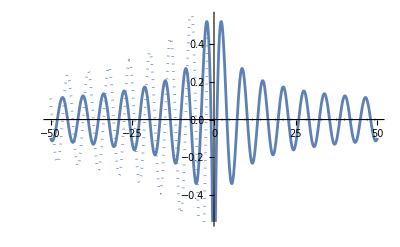

```mathematica
ReImPlot[BesselY[0,x],{x,-50,50}]
```

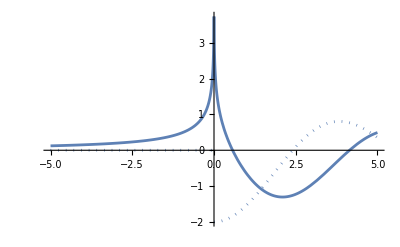

```mathematica
ReImPlot[StruveH[0,-x]-BesselY[0,-x],{x,-5,5}]
```

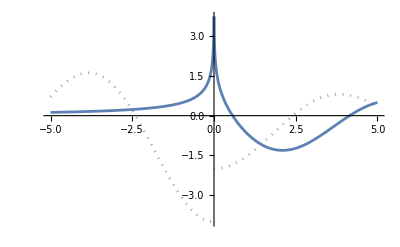

```mathematica
ReImPlot[-StruveH[0,x]-BesselY[0,x]-2I BesselJ[0,x],{x,-5,5}]
```

```mathematica
x = 3 + 2I;
N[StruveH[0,x]-BesselY[0,x]];
N[BesselJ[0,x] + I*StruveH[0,x]]
```

0.0700183+0.19884 ⅈ

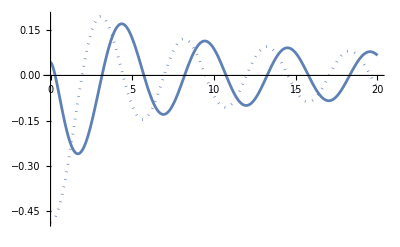

```mathematica
b = 2;
g = -0.5;
p0 =( y^5 -b y+g == 0);
rts = List @@ NRoots[p0,y][[All,2]];
pf = 1./ (5*rts^4-b);
ReImPlot[Sum[Pi/2 pf[[i]]rts[[i]]^2*(StruveH[0,-rts[[i]]*x] - BesselY[0,-rts[[i]]*x]),{i,1,5}] ,{x, 0, 20}]
```

```mathematica
b = 2;
g = -0.5;
p0 =( y^5 -b y+g == 0);
rts = List @@ NRoots[p0,y][[All,2]];
pf = 1./ (5*rts^4-b);
ReImPlot[Sum[Pi/2 pf[[i]]rts[[i]]^2*(StruveH[0,-rts[[i]]*x] - BesselY[0,-rts[[i]]*x]),{i,1,5}] ,{x, 0, 20}]
```

```mathematica
rts
```

{-0.910273-0.608707 ⅈ,-0.910273+0.608707 ⅈ,0.304724-1.13327 ⅈ,0.304724+1.13327 ⅈ,1.2111}

```mathematica
N[StruveH[0,-rts[[3]]]-BesselY[0,-rts[[3]]]]
```

0.118432-0.598192 ⅈ

```mathematica
N[StruveH[0,-rts[[5]]]-BesselY[0,-rts[[5]]]]
```

-0.887443-1.33117 ⅈ

```mathematica
rts[[5]]
```

1.2111

```mathematica
x =3 - 2I;
N[StruveH[0,-x]-BesselY[0,-x]]
```

-0.25166-0.0522251 ⅈ

```mathematica
x =3 ;
N[StruveH[0,-x]-BesselY[0,-x]]
```

-0.951156+0.520104 ⅈ

```mathematica
x =-2 ;
N[StruveH[0,x]-BesselY[0,x]]
```

-1.30123-0.447782 ⅈ

```mathematica
x =2 ;
N[StruveH[1,x]-BesselY[1,x]]
```

0.753796

```mathematica
x =-2-2I ;
N[StruveH[1,x]-BesselY[1,x]]
```

0.562762-0.179132 ⅈ

```mathematica
x =-2+I;
N[BesselJ[1,x]+I StruveH[1,x]]
```

-0.261584+0.611786 ⅈ

```mathematica
x =2+I ;
N[StruveH[1,x]-BesselY[1,x]]
```

0.708034-0.0703676 ⅈ

```mathematica
FourierTransform[1/(-rho - rhoj), rho, xi]
```

ⅈ ⅇ^(-ⅈ rhoj xi) √(π/2) (Sign[xi] (-1+Sign[Abs[Im[rhoj]]])+2 HeavisideTheta[-xi Sign[Im[rhoj]]] Sign[Im[rhoj]])

```mathematica
Integrate[BesselJ[0, q]*Exp[-I*xi*q],{q, -Infinity,  Infinity}]
```

ConditionalExpression[2/(√(1-xi^2)), -1<Re[xi]<1&&Im[xi]==0]

```mathematica
Integrate[2*Rectangle[xi/2]/(1-xi^2)*Exp[I*xi*x],{x,-Infinity,Infinity}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {2+ⅈ,-∞,∞}.

∫_(-∞)^∞ (2 ⅇ^((-1+2 ⅈ) xi) Rectangle[xi/2])/(1-xi^2)ⅆ(2+ⅈ)